```mathematica
(x-5)^2+(y-5)^2==25
```

(-5+x)^2+(-5+y)^2==25

```mathematica
Solve[(-5+x)^2+(-5+y)^2==25,y]
```

{{y→5-√(10 x-x^2)},{y→5+√(10 x-x^2)}}

```mathematica
a=5-Sqrt[10x-x^2]
```

5-√(10 x-x^2)

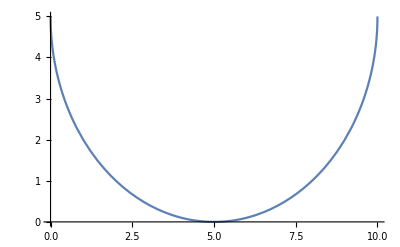

```mathematica
Plot[5-√(10 x-x^2),{x,0,10}]
```

```mathematica
Solve[a==1/2 x,x]
```

{{x→2},{x→10}}

```mathematica
S1=Integrate[a-1/2 x,{x,0,2}]
```

15-(25 π)/2+25 ArcSin[2/(√5)]

```mathematica
S2=(10^2-Pi*5^2)/4-S1
```

-15+1/4 (100-25 π)+(25 π)/2-25 ArcSin[2/(√5)]

```mathematica
S=(10 20-2 *Pi* 5^2 )/2-S2
```

15+1/2 (200-50 π)-(25 π)/2+1/4 (-100+25 π)+25 ArcSin[2/(√5)]

```mathematica
S//Simplify
```

90-(125 π)/4+25 ArcSin[2/(√5)]

```mathematica
N[S,10]
```

19.50394752